```mathematica
SetDirectory[NotebookDirectory[]];
<<MeshTools.wl
SolutionDirectory="solutions/";
MeshDirectory="meshes/";
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Annulus[{0,0},{1,1.5}],"BoundaryMarkerFunction"->Function[{coords,points},If[Norm[#//Mean]>1,5,6]&/@coords]],ToBoundaryMesh[Rectangle[{-3,-3},{3,3}]]];
air={{0,0},{0,2}};
dielectric={0,1.25};
mesh=ToElementMeshDefault[bmesh,Append[{#,1}&/@air,{dielectric,2}]];
```

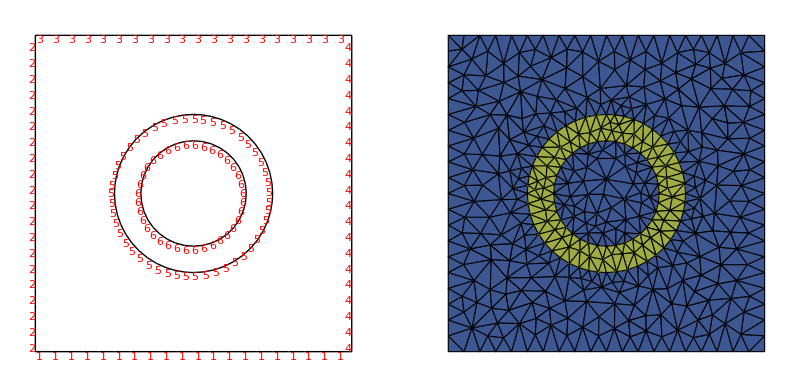

```mathematica
MeshInspect[mesh]
```

```mathematica
InterpAndShow[Import[SolutionDirectory<>"annulus_dielectric.txt","Data"],Annulus[{0,0},{1,1.5}]]
```

-Graphics-

```mathematica
mesh=ReadMesh[MeshDirectory<>"cylinder-in-square.tmh"]
```

ElementMesh[{{-3.,3.},{-3.,3.}},{TriangleElement[<908>]}]

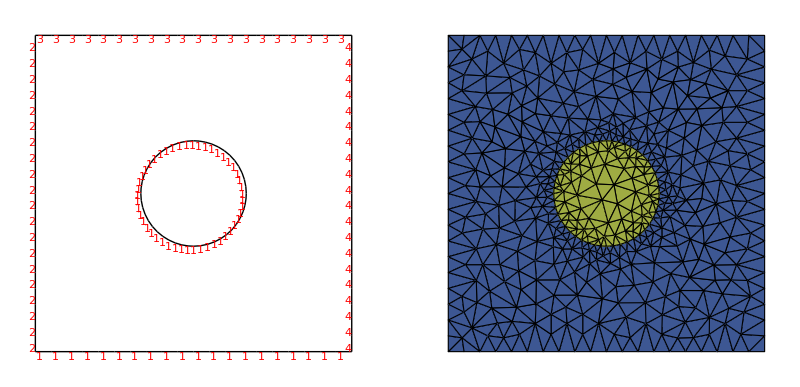

```mathematica
mesh//MeshInspect
```

```mathematica
(*Magnetized Rod*)
```

```mathematica
A=NDSolveValue[{a[x,y]{x,y}==Piecewise[{{y^2/(√(x^2+y^2)),x^2+y^2≤1}},0],DirichletCondition[a[x,y]==y^2/(2 (x^2+y^2)),x^2+y^2>2]},a,{x,y}∈mesh]
```

InterpolatingFunction[…]

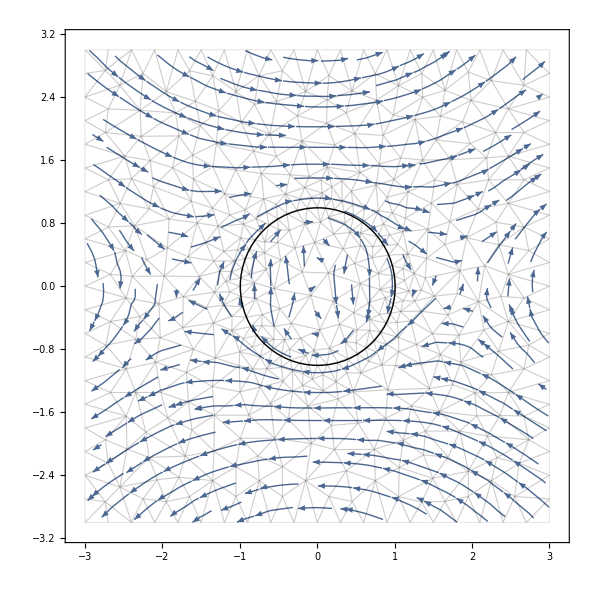

```mathematica
Show[StreamPlot[Evaluate[({0,0,A[x,y]}{x,y,z})⟦1;;2⟧],{x,y}∈mesh],Graphics[{FaceForm[None],EdgeForm[{Thin,Opacity[.1]}],DiscretizeGraphics[mesh["Wireframe"]],Circle[]}]]
```

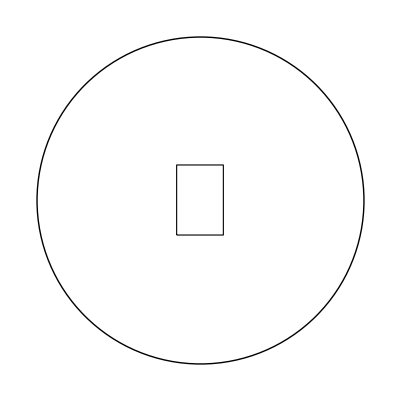

```mathematica
Graphics[{EdgeForm[Thin],FaceForm[None],Rectangle[{-1/10,-.15},{1/10,.15}],Circle[{0,0},.7]}]
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh@Rectangle[{-1/10,-.15},{1/10,.15}],ToBoundaryMesh@Circle[{0,0},.7]]
```

ElementMesh[{{-0.7,0.7},{-0.7,0.7}},Automatic]

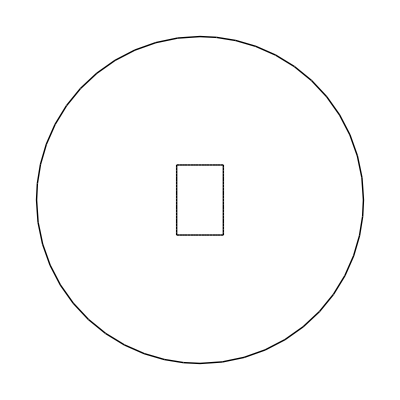

```mathematica
bmesh["Wireframe"]
```

```mathematica
.4Sqrt[2]
```

0.565685

```mathematica
mesh=ToElementMesh[bmesh,"RegionMarker"->{{{0,0},2},{{.4,.4},1}}]
```

ElementMesh[{{-0.7,0.7},{-0.7,0.7}},{TriangleElement[<1194>]}]

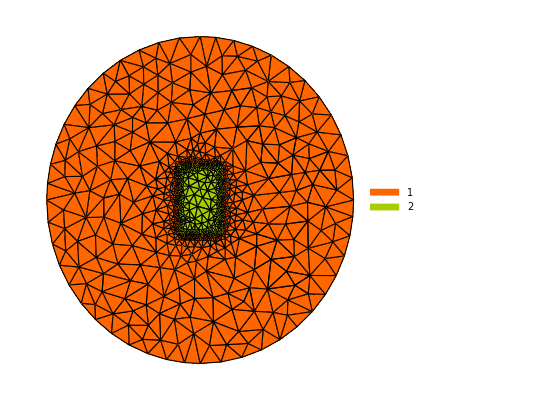

```mathematica
MeshInspect[mesh]
```

```mathematica
Subscript[μ, 0]=4*Pi*10^(-7)
```

π/2500000

```mathematica
ν=-IdentityMatrix[2]*Piecewise[{{1/Subscript[μ, 0]*1.05,ElementMarker==2}},1/Subscript[μ, 0]]
```

{{-(Piecewise[{{835563., ElementMarker==2}, {2500000/π, True}}]),0},{0,-(Piecewise[{{835563., ElementMarker==2}, {2500000/π, True}}])}}

```mathematica
w=0.01;
pde=Inactive[Div][Inactive[Dot][ν,Inactive[Grad][a[x,y],{x,y}]],{x,y}]==Piecewise[{{1000000/(w)*Sign[x],And[1/10-w/2<Abs[x]<1/10+w/2,Abs[y]<=.15]}},0]
bcs=DirichletCondition[a[x,y]==0,x^2+y^2>.3];
A=NDSolveValue[{pde,bcs},a,{x,y}∈mesh]
Evaluate[-Curl[A[x,y],{x,y}]]/.{x->0,y->0};
Norm[%]
```

({{-(Piecewise[{{835563., ElementMarker==2}, {2500000/π, True}}]),0},{0,-(Piecewise[{{835563., ElementMarker==2}, {2500000/π, True}}])}}.a[x,y]{x,y}Inactive){x,y}Inactive==(Piecewise[{{1.×10^8 Sign[x], 0.095<Abs[x]<0.105&&Abs[y]≤0.15}, {0, True}}])

InterpolatingFunction[…]

0.712983

InterpolatingFunction[…]

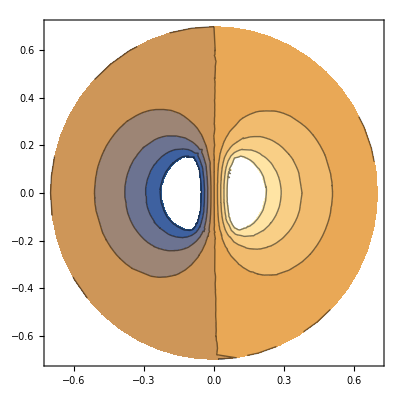

```mathematica
ContourPlot[A[x,y],{x,y}∈mesh]
```

```mathematica
r=0.015
```

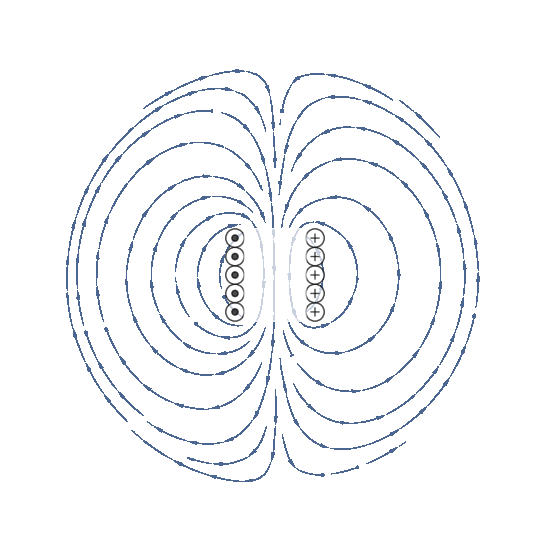

{-0.00703411,-0.817548}

0.817578

```mathematica
Show[StreamPlot[Evaluate[-Curl[A[x,y],{x,y}]],{x,y}∈mesh,StreamMarkers->"PinDart",PlotTheme->"Minimal",StreamPoints->20,ColorFunction->Hue],Graphics[{Opacity[.7],White,EdgeForm[{Black,Thickness[.002]}],Table[{Disk[{x,-1/10-2 r}//Reverse,2 r],Black,Disk[{x,-1/10-2 r}//Reverse,(2 r)/3],White,Disk[{x,1/10+2 r}//Reverse,2 r],Black,Line[Reverse/@{{x-r,1/10+2 r},{x+r,1/10+2 r}}],Line[Reverse/@{{x,1/10+r},{x,1/10+3 r}}]},{x,-.15+2r,+.15-2r,4r}],FaceForm[White],EdgeForm[Thickness[.002]],Rectangle[{-1/10+.001,-.15},{1/10,.15}]}]]
```

```mathematica
2000/1.4
```

1428.57

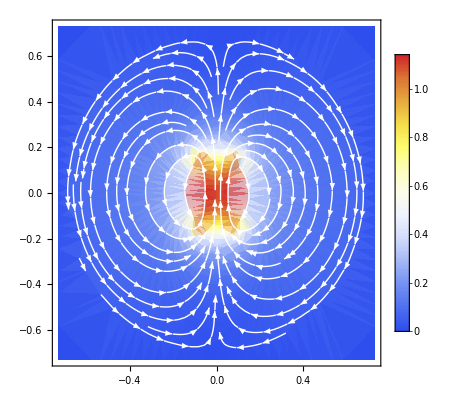

```mathematica
StreamDensityPlot[Evaluate[-Curl[A[x,y],{x,y}]],{x,y}∈mesh,ColorFunction->"TemperatureMap",PlotRange->Full,PlotLegends->Automatic,StreamColorFunction->Function[x,White]]
```

```mathematica
Clear[x]
```

```mathematica
x=
```

```mathematica
-0.12==-.15+2r
```

-0.12==-0.15+2 r

0.015

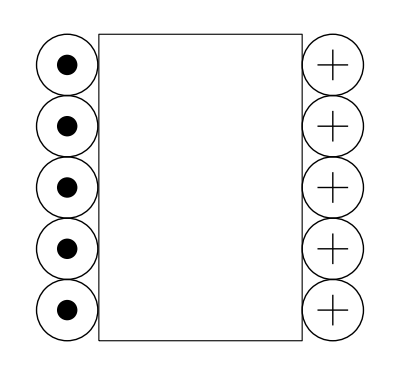

```mathematica
Solve[-0.12==-0.15+2 r,{r}]
```

```mathematica
TransformedField["Polar"->"Cartesian",20/(3)(r-1)-1,{r,t}->{x,y}]
```

1/3 (-23+20 √(x^2+y^2))

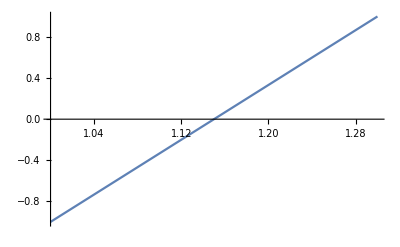

```mathematica
Plot[(2 (r-1))/(.3)-1,{r,1,1.3}]
```

```mathematica
Color
```

```mathematica
mesh
```

mesh

```mathematica
Show[DensityPlot[Cos[3ArcTan[x,y]],{x,y}∈Annulus[{0,0},{1,1.3}],ColorFunction->"RedBlueTones",PlotTheme->"Minimal"],Graphics[{FaceForm[None],EdgeForm[Black],Table[Rotate[Annulus[{0,0},{1,1.3},{Pi/3+.01,2Pi/3-.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}],FaceForm[White],Table[Rotate[Annulus[{0,0},{1,1.3},{-.01,+.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}]}]]
```

-Graphics-

```mathematica
Color
```

```mathematica
Graphics[Table[Rotate[Annulus[{0,0},{1,1.3},{Pi/3+.01,2Pi/3-.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}]]
```

EmptyRegion[2]

```mathematica
?SquareWave
```

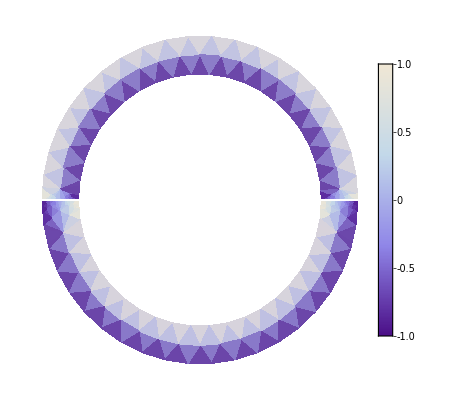

```mathematica
DensityPlot[current,{x,y}∈Annulus[{0,0},{1,1.3}],PlotTheme->"Minimal",ColorFunction->"FushiaTones",PlotLegends->Automatic]
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Disk[{0,0},5]],ToBoundaryMesh[Annulus[{0,0},{1,1.3}]]]
```

ElementMesh[{{-5.,5.},{-5.,5.}},Automatic]

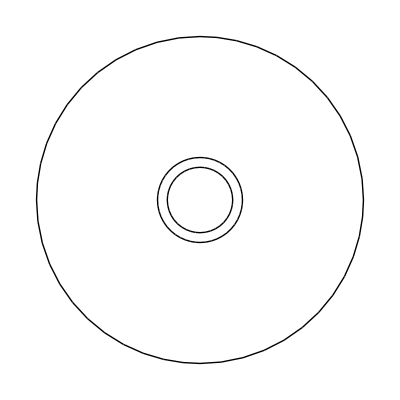

```mathematica
bmesh["Wireframe"]
```

```mathematica
mesh=ToElementMesh[bmesh,"RegionMarker"->{{{0,0},2},{{0,4},1},{{0,1.2},3}},MaxCellMeasure->Automatic,"NodeReordering"->True,"MeshOrder"->2]
```

ElementMesh[{{-5.,5.},{-5.,5.}},{TriangleElement[<912>]}]

```mathematica
ExportMesh[MeshDirectory<>"ring.tmh",mesh]
```

meshes/ring.tmh

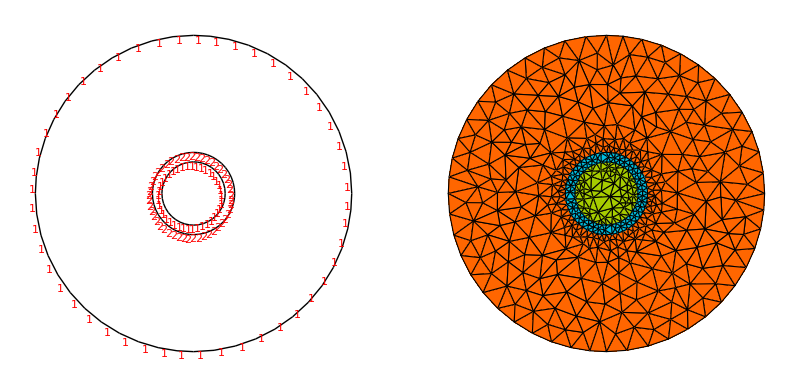

```mathematica
MeshInspect[mesh]
```

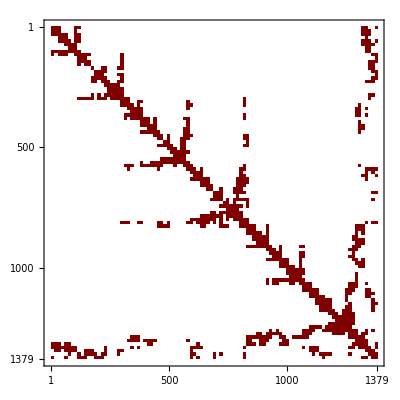

```mathematica
PlotIncidence[mesh]
```

```mathematica
μAir=4 π*10^-7;
HField={10,25,50,75,108,137,160,180,200,235,285,320,365,480,560,660,800,1000,1150,1550,1840,2250,2800,3450,4350,5500,7707,11863,15839,21076,27281,35289,45642,59046,76413,98907,128000,134764,141880,149364,157235};
BField={0.0025,0.0066,0.0151,0.0264,0.05,0.1,0.15,0.2,0.25,0.35,0.5,0.6,0.7,0.9,1.,1.1,1.2,1.3,1.354,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.81,1.89,1.945,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.36,2.37,2.38,2.39};
BHData=Transpose[{BField,BField/HField}];
model=a1 Exp[-(x-b1)^2/(c1^2)]+a2/(1+Exp[(x-b2)^2/(c2^2)])^2;
fitData=FindFit[BHData,model,{a1,b1,c1,a2,b2,c2},x];
fit=Function[x,model/.fitData];
B2Norm=Sqrt[Total[Grad[a[x,y],{x,y}]^2]+$MachineEpsilon];
```

```mathematica
ν=Piecewise[{{-1/fit[B2Norm],ElementMarker==4}},-1/μAir]*IdentityMatrix[2];
```

```mathematica
current=SquareWave[ArcTan[x,y]/(2π/3)+1/4] 1/3 (-23+20 √(x^2+y^2));
```

```mathematica
pde=Inactive[Div][Inactive[Dot][IdentityMatrix[2],Inactive[Grad][a[x,y],{x,y}]],{x,y}]==Piecewise[{{TriangleWave[ArcTan[x,y]/(2*Pi/3)+1/4],ElementMarker==3},{0,ElementMarker==2}},0];
```

```mathematica
bcs=DirichletCondition[a[x,y]==0,x^2+y^2≥20];
```

```mathematica
AbsoluteTiming[A=NDSolveValue[{pde,bcs},a,{x,y}∈mesh]]
```

{0.087657,InterpolatingFunction[…]}

```mathematica
Show[StreamPlot[Curl[A[x,y],{x,y}]//Evaluate,{x,y}∈mesh,StreamScale->Tiny,StreamPoints->Fine,PlotTheme->"Minimal"],Graphics[{FaceForm[None],EdgeForm[Black],Annulus[{0,0},{1,1.3}]}]]
```

-Graphics-

```mathematica
Plot3D[A[x,y],{x,y}∈mesh,PlotRange->Full]
```

-Graphics3D-

```mathematica
pde=Inactive[Div][Inactive[Dot][ν,Inactive[Grad][a[x,y],{x,y}]],{x,y}]==Piecewise[{{x,{x,y}∈Rectangle[{-3,-1},{3,1}]}},0];
bcs=DirichletCondition[a[x,y]==Log[x^2+y^2]/2,x^2+y^2≥100];
```

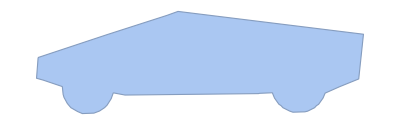
```mathematica
cybertruck=-Graphics-//RescaleRegion
```

```mathematica
-Graphics-//BoundingRegion
```

Cuboid[{-3.1875,-1.},{3.1875,1.}]

```mathematica
U=NDSolveValue[{Laplacian[u[x,y],{x,y}]==0,DirichletCondition[u[x,y]==Sign[x],Abs[x]≥5]},u,{x,y}∈mesh]
```

InterpolatingFunction[…]

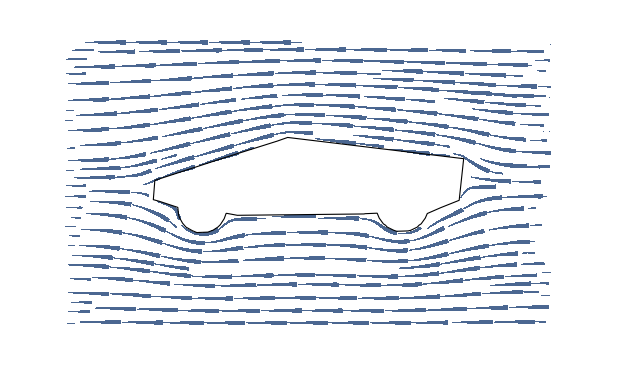

```mathematica
Show[StreamPlot[Grad[U[x,y],{x,y}]//Evaluate,{x,y}∈mesh,AspectRatio->3/5,PlotTheme->"Minimal",StreamPoints->Fine,StreamMarkers->"BackwardPointer",ColorFunction->Hue],Graphics[{FaceForm[None],EdgeForm[{Black,Thick}],cybertruck}]]
```

```mathematica
data=Import[SolutionDirectory<>"bldc_nonlinear.txt","Data"];
```

```mathematica
data//Dimensions
```

{2625,3}

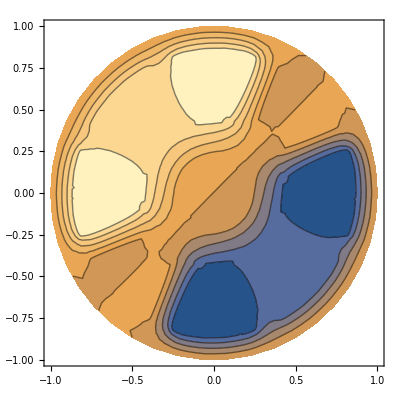

```mathematica
ListContourPlot[data]
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
A=Interpolation[data]
```

InterpolatingFunction[…]

```mathematica
{minsol,maxsol}=MinMax[A["ValuesOnGrid"]]
```

{-4.89051×10^-7,4.88386×10^-7}

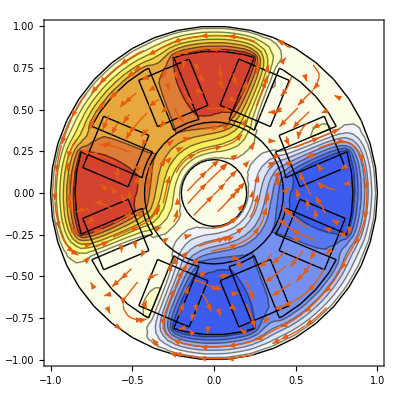

```mathematica
Show[ContourPlot[A[x,y],{x,y}∈mesh,PlotRange->All,Contours->Range[minsol,maxsol,(maxsol-minsol)/15],ColorFunction->"TemperatureMap"],bmesh["Wireframe"],StreamPlot[Evaluate[{{0,1},{-1,0}}.Grad[A[x,y],{x,y}]],{x,y}∈mesh,StreamPoints->200,PlotTheme->"Scientific"]]
```

```mathematica
Plot3D[Grad[A[x,y],{x,y}]//Norm//Evaluate,{x,y}∈mesh]
```

-Graphics3D-